-Graphics-

# Image Processing

```mathematica
FlipView[
{-Graphics-,DynamicModule[
{cloony=-Graphics-,cpos={55.,81.} ,csize={{98.,98.}},img,face, pos={160,120}, size,scale=1},
Dynamic[
img = CurrentImage[];
face = List@@First[FindFaces[img],face];
pos=0.5pos+0.5Mean@face;
size=Differences@face;
scale = 0.8scale+0.2Apply[Mean,size/csize];
ImageCompose[img,ImageResize[cloony,Scaled[scale]],pos,scale cpos]
]
]}]
```

-Graphics-

## Learning Objectives

In this lecture you will learn about image processing as such and about the image framework in the Wolfram Language.

Topics include morphology, feature detection, filters, segmentation, geometric transformations, and image recognition.

## Outline

### Image and Image3D

### Spatial Operations

### Morphology

### Filters & Features

### Image Registration

### Image Segmentation

## Image Import

### File Import

Images usually come in files.

The commonly used image file formats are JPEG, TIFF, and PNG.

You can import images into a Wolfram Notebook^™ by using drag and drop, copy and paste, or the Import command.

Import a 2D image stored in a TIFF file.

```mathematica
Import["ExampleData/lena.tif"]
```

Import a 3D volume stored in a multiform TIFF file.

```mathematica
Import["ExampleData/CTengine.tiff","Image3D"]
```

## Image Import

### Camera Feeds

You can also capture images directly from connected devices, such as built-in webcams.

Connect to and open a device:

```mathematica
dev=DeviceOpen["Camera"]
```

Read image data from the device:

```mathematica
DeviceRead[dev]
```

Close the device once the acquisition is done.

```mathematica
DeviceClose["Camera"]
```

CurrentImage does the above in one stroke:

```mathematica
CurrentImage[]
```

## Image Import

### Curated Databases

The Wolfram Language includes a large number of curated databases. Images are available for many entities.

Retrieve an image associated to an entity:

```mathematica
EntityValue[LinguisticAssistant,"Image"]
```

Images associated with multiple entities:

```mathematica
EntityValue[LakeData["SampleEntities"],EntityProperty["Lake","Image"],"EntityAssociation"]
```

```mathematica
ImageCollage[EntityValue[LakeData["SampleEntities"],EntityProperty["Lake","Image"]],ImagePadding->2,Background->White]
```

## Image Generation

### Rasterize

You can rasterize any expression, such as plots or equations into an image.

Create a vector graphic:

```mathematica
expr=Plot[{Sin[x],Cos[x]},{x,0,3π}]
```

Rasterize into an image:

```mathematica
img=Rasterize[expr]
```

Apply an image processing operation:

```mathematica
Blur[img,8]
```

## Image Generation

### Array to Image

2D and 3D images can be created directly from arrays of pixel values.

Create a single-channel 2D image from a 2D array of byte values between 0 and 255:

```mathematica
Image[({{161, 115, 124, 141, 155, 164, 171, 179, 181, 183, 175, 171, 172, 168, 163, 156, 154, 174, 177, 130}, {134, 139, 143, 154, 177, 204, 207, 219, 204, 211, 220, 191, 182, 176, 173, 171, 163, 153, 147, 136}, {121, 145, 156, 160, 184, 219, 232, 238, 237, 215, 213, 208, 197, 192, 188, 207, 212, 177, 154, 144}, {131, 148, 170, 180, 187, 200, 207, 215, 223, 222, 220, 210, 203, 205, 209, 218, 229, 198, 168, 164}, {139, 164, 181, 195, 202, 210, 203, 197, 216, 222, 208, 216, 225, 213, 215, 196, 193, 197, 180, 171}, {147, 128, 163, 189, 202, 198, 101, 122, 211, 219, 175, 178, 143, 198, 181, 190, 194, 185, 177, 145}, {145, 79, 149, 190, 190, 179, 134, 149, 204, 190, 137, 154, 53, 154, 137, 177, 176, 160, 154, 141}, {122, 146, 152, 165, 169, 154, 128, 148, 184, 120, 144, 158, 42, 124, 138, 155, 117, 88, 70, 69}, {99, 131, 149, 118, 117, 97, 104, 127, 124, 47, 104, 158, 94, 91, 116, 147, 86, 77, 65, 42}, {60, 66, 88, 111, 107, 104, 111, 90, 92, 101, 92, 92, 90, 75, 73, 71, 67, 59, 52, 43}, {51, 56, 67, 74, 74, 77, 82, 80, 78, 83, 81, 77, 75, 71, 61, 56, 50, 39, 35, 27}, {37, 46, 57, 60, 64, 75, 76, 77, 73, 73, 74, 76, 63, 59, 57, 42, 41, 37, 26, 21}, {34, 47, 54, 58, 62, 62, 63, 67, 65, 57, 57, 57, 55, 50, 42, 35, 24, 22, 18, 18}}),"Byte",Magnification->10]
```

Create a single-channel 3D image from a 3D array:

```mathematica
Image3D[{({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}}),({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 104, 147, 180, 147, 104, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}}),({{0, 0, 0, 104, 0, 0, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 104, 147, 180, 147, 104, 0}, {104, 147, 180, 255, 180, 147, 104}, {0, 104, 147, 180, 147, 104, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 0, 0, 104, 0, 0, 0}}),({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 104, 147, 180, 147, 104, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}}),({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 104, 147, 104, 0, 0}, {0, 0, 0, 104, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})},"Byte"]
```

## Image Export

### Image to Array

Convert an Image into a Real-valued array :

```mathematica
ImageData[-Graphics-]//MatrixForm
```

Convert an Image into a Byte array with values ranging from 0 to 255:

```mathematica
ImageData[-Graphics-,"Byte"]//MatrixForm
```

### Pixel Values

A single pixel value of a color image:

```mathematica
PixelValue[-Graphics-,{10,10}]
```

Multiple pixel values:

```mathematica
PixelValue[-Graphics-,{{10,10},{20,20},{30,30},{40,40},{50,50}}]
```

Pixel values at positions specified by a marker image:

```mathematica
PixelValue[-Graphics-,-Graphics-]
```

## Image Export

### Saving Image Files

Images can also be exported to various file formats.

Export a 2D image to a JPEG file:

```mathematica
Export["landscape.jpg",-Graphics-]
```

Export a 3D image to a multiframe TIFF file:

```mathematica
Export["corns.tiff",-Graphics3D-]
```

Import the 3D image again:

```mathematica
Import["corns.tiff"]
```

```mathematica
Import["corns.tiff","Image3D"]
```

## Image Properties

### Image Type

You can store 2D and 3D images with different bit depths. Common bit depths are 8 bit and 16 bit (high color); 24 bit (true color); and 30, 36, and 48 bit (deep color).

The following bit depths are supported in the Wolfram Language:

```mathematica
Panel[TableForm[{{"\"Bit\"", "1", "integer 0 or 1", "yes", "yes"}, 
    {"\"Byte\"", "1", "integer 0 through 255", "yes", "yes"}, 
    {"\"Bit16\"", "2", "integer 0 through 65535", "yes", "yes"}, 
    {"\"Real32\"", "4", "single precision real (32-bit)", "no", "no"}, 
    {"\"Real64\"", "8", "double precision real (64-bit)", "no", "no"}}, 
   TableHeadings -> {None, {"type", "bytes per pixel channel", "data range", "clipping", 
      "quantization"}}, TableSpacing -> {1.5, 4}], BaseStyle -> "Text"]
```

type | bytes per pixel channel | data range | clipping | quantization
"Bit" | 1 | integer 0 or 1 | yes | yes
"Byte" | 1 | integer 0 through 255 | yes | yes
"Bit16" | 2 | integer 0 through 65535 | yes | yes
"Real32" | 4 | single precision real (32-bit) | no | no
"Real64" | 8 | double precision real (64-bit) | no | no

Data type of an image:

```mathematica
ImageType[-Graphics-]
```

A smaller bit depth reduces the memory consumption:

```mathematica
Panel[TableForm[Table[{type,Quantity[ByteCount[Image[-Graphics-,type]]/2^20//N,"MB"]},{type,{"Byte","Bit16","Real32","Real64"}}],TableHeadings -> {None, {"data type", "byte count"}},TableSpacing -> {1.5, 4}], BaseStyle -> "Text"]
```

data type | byte count
Byte | 0.62606 MB
Bit16 | 1.2517 MB
Real32 | 2.50298 MB
Real64 | 5.00553 MB

Note that the pixel value range is also limited by using smaller bit depths. For example, Byte images can only store integer values between 0 and 255. All real values in the range are quantized, and any value outside the range will be clipped and cannot be restored. On the other hand, single- and double-precision real data types can store almost any values.

Multiply pixel values of a byte and a real image by 2:

```mathematica
img=-Graphics-;
```

```mathematica
result=Table[2 Image[img,type],{type,{"Byte","Real"}}];
GraphicsRow[result]
```

Notice the out-of-range values in the real image:

```mathematica
Map[ImageHistogram[#,All,ImageSize->300]&,result]//GraphicsRow
```

You can bring the pixel values of the real-valued image back into the visible range:

```mathematica
Map[ImageAdjust,result] // GraphicsRow
```

## Image Properties

### Color Spaces

An image color space specifies how to interpret channel values of an image.

Common color spaces are grayscale, RGB, CMYK, and HSB. These color spaces are all device-dependent and perceptually nonlinear.

Common device-independent color spaces are XYZ and LAB. An image color space can also be specified using a color profile.

The following color spaces are supported in the Wolfram Language.

```mathematica
{{"color space", "description", "deviceindependent"}, {"\"Grayscale\"", "gray level", "no"}, {"\"RGB\"", "red, green, blue", "no"}, {"\"CMYK\"", "cyan, magenta, yellow, black", "no"}, {"\"HSB\"", "\!\(\*Cell[\"hue, saturation, brightness\", \"TableText\"]\)", "no"}, {"\"XYZ\"", "CIE XYZ", "yes"}, {"\"LAB\"", "CIE \!\(TraditionalForm\`\*SuperscriptBox[\(L\), \(*\)] \*SuperscriptBox[\(a\), \(*\)] \*SuperscriptBox[\(b\), \(*\)]\)", "yes"}, {"\"LCH\"", "CIE \!\(\*FormBox[SuperscriptBox[\"L\", \n  StyleBox[\"*\",\nFontSize->10]],\n TraditionalForm]\)\!\(\*FormBox[SuperscriptBox[\"C\", \n  StyleBox[\"*\",\nFontSize->10]],\n TraditionalForm]\)\!\(\*FormBox[\n RowBox[{\"h\", \"(\", \n  RowBox[{SuperscriptBox[\"a\", \n    StyleBox[\"*\",\nFontSize->10]], SuperscriptBox[\"b\", \n    StyleBox[\"*\",\nFontSize->10]]}], \")\"}],\n TraditionalForm]\)", "yes"}, {"\"LUV\"", "CIE \!\(TraditionalForm\`\*SuperscriptBox[\(L\), \(*\)] \*SuperscriptBox[\(u\), \(*\)] \*SuperscriptBox[\(v\), \(*\)]\)", "yes"}, {Automatic, "no color space specified", "no"}}
```

Color space is stored as an option in the image:

```mathematica
img=-Graphics-;
```

Extract image color space:

```mathematica
ImageColorSpace[img]
```

RGB

Construct an image from the same data in different color spaces:

```mathematica
data=ImageData[img];
```

```mathematica
Table[Labeled[Image[data,ColorSpace->cs],Text[cs]],{cs,{"RGB","HSB","XYZ","LAB","LCH","LUV"} }]
```

Create an image using a specific color profile:

```mathematica
img=Image[data,ColorSpace->Import["sRGB_v4_ICC_preference.icc"]]
```

Convert to the LAB color space:

```mathematica
ColorConvert[img,"LAB"]
```

## Image Properties

### Color Channels

Images can contain multiple channels of information. An n-channel image stores n values per pixel.

For specific color spaces, such as RGB, channel values encode color.

You can also introduce an arbitrary number of channels which can represent any property.

Extract the number of channels of an image:

```mathematica
ImageChannels[-Graphics-]
```

Combine multiple single-channel images into one image:

```mathematica
ColorCombine[{-Graphics-,-Graphics-,-Graphics-},"RGB"]
```

Generate a 12-channel random image:

```mathematica
img12=Image[RandomReal[1,{10,10,12}],Magnification->10]
```

Channel values of pixel at position {2.5, 3.5}:

```mathematica
ImageValue[img12,{2.5,3.5}]
```

## Image Properties

### Alpha Channel

An α-channel does not determine color but opacity. Fully opaque pixels have an α-value of 1. Fully transparent pixels have an α-value of 0.

Set opacity of pixels by adding an alpha channel:

```mathematica
img=SetAlphaChannel[-Graphics-,-Graphics-]
```

You can remove opacity by blending all pixels with a background color or image:

```mathematica
GraphicsRow[Table[Labeled[RemoveAlphaChannel[img,color],color],{color,{White,Blue,Yellow,Black}}],ImageSize->600]
```

## Image Properties

### Interleaving or Planar

Interleaving specifies the order in which image data is stored.

In an interleaved setting, the data is organized as a 2D array of lists of color values.

In a planar setting, the data is stored as n 2D arrays of scalar values where n denotes the number of channels.

#### Planar Images

```mathematica
data = {{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}},{{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}},{{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}}};
TableForm[{{MatrixForm[MatrixForm/@data,TableDirections->Row],MatrixForm[Transpose[data, {3, 2, 1}], TableDepth->2]}},TableDepth->2,TableHeadings->{None,Text/@{"Planar","Interleaved"}}]
```

Planar | Interleaved
((RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]) | (RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]) | (RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1])) | ({RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]})

```mathematica
Options[-Graphics-,Interleaving]
```

```mathematica
Map[MatrixForm,ImageData[-Graphics-,Interleaving->False]]
```

Create an image from data in which color channels are represented in planar form:

```mathematica
Image[RandomReal[1,{3,10,10}],Interleaving->False,Magnification->10]
```

#### Interleaved Images

```mathematica
MatrixForm[Transpose[data, {3, 2, 1}], TableDepth->2]
```

({RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]})

```mathematica
Options[-Graphics-,Interleaving]
```

```mathematica
{Interleaving->True}
```

```mathematica
ImageData[-Graphics-]//MatrixForm
```

Create an image from data in which color channels are represented in interleaved form:

```mathematica
Image[RandomReal[1,{10,10,3}],Interleaving->True,Magnification->10]
```

Note: Images are not equal, if there is a difference in their interleaving setting:

```mathematica
Image[img,Interleaving->True]==Image[img,Interleaving->False]
```

## Image Coordinate Systems

There are two coordinate systems used in image processing and analysis, the matrix coordinate system and the graphics coordinate system:

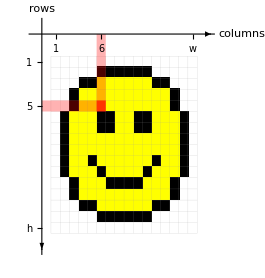
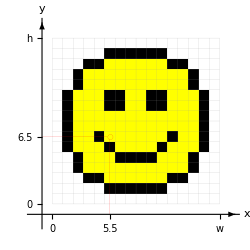
matrix coordinate | graphics coordinate
-Graphics- | -Graphics-

```mathematica
g1=Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-1.5,19}},
AxesOrigin->{-1,18},
AxesLabel-> {"columns","rows"} ,
Ticks->{
Join[{{0.5,1}},{{5.5,6}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,HoldForm[w]}}],
Join[{{0.5,HoldForm[h]}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,1}},{{11.5,5}}]
} , 
Epilog -> {
Arrow[{{17.4,18},{17.5,18}}],
Arrow[{{-1,-1.4},{-1,-1.5}}],
{Red,Thickness[0],
(*Line[{{-1,11.5},{5.25,11.5}}],Line[{{5.5,11.75},{5.5,18}}],*)
(*Circle[{5.5,11.5},1/4],*)
Opacity[.3],Rectangle[{-1,11},{5,12}],Rectangle[{5,11},{6,18}],
Opacity[.7],Rectangle[{5,11},{6,12}]
}
}
,ImageSize->265];
g2=Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,5.5,{16,HoldForm[w]}},
{0,6.5,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{Red,Thickness[0],
Line[{{-1,6.5},{5.25,6.5}}],Line[{{5.5,6.25},{5.5,-1}}],
Circle[{5.5,6.5},1/4]}
}
,ImageSize->250];
g3=Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0],  GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,{16,1}},
{0,{16,HoldForm[h/w]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}]
},ImageSize->200];
g4=Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0],  GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
Join[{{0,"",{0.04,-0.01}},{0.5,1}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,HoldForm[w]},{16,"",{0.04,-0.01}}}],
Join[{{0,"",{0.04,-0.01}},{0.5,1}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,HoldForm[h]},{16,"",{0.04,-0.01}}}]
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}]
},ImageSize->200];
TableForm[{{g1,g2(*,g3,g4*)}},TableHeadings->{None,Text/@{"matrix coordinate","graphics coordinate"(*,"scaled graphics","pixel-aligned graphics"*)}}]
```

## Image Coordinate Systems

### Matrix or Index Coordinates

The matrix coordinate space reflects the data matrix stored in the image. The matrix is stored in rows of columns of pixel values. Therefore, pixel locations are the same as their corresponding row and column in the data matrix, where rows run from top to bottom and columns run from left to right.

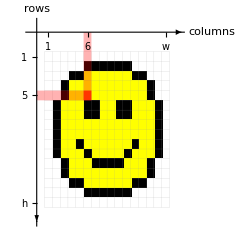

```mathematica
g1=Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-1.5,19}},
AxesOrigin->{-1,18},
AxesLabel-> {"columns","rows"} ,
Ticks->{
Join[{{0.5,1}},{{5.5,6}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,HoldForm[w]}}],
Join[{{0.5,HoldForm[h]}},Table[{k,""},{k,1.5,14.5,1}],{{15.5,1}},{{11.5,5}}]
} , 
Epilog -> {
Arrow[{{17.4,18},{17.5,18}}],
Arrow[{{-1,-1.4},{-1,-1.5}}],
{Red,Thickness[0],
(*Line[{{-1,11.5},{5.25,11.5}}],Line[{{5.5,11.75},{5.5,18}}],*)
(*Circle[{5.5,11.5},1/4],*)
Opacity[.3],Rectangle[{-1,11},{5,12}],Rectangle[{5,11},{6,18}],
Opacity[.7],Rectangle[{5,11},{6,12}]
}
}
,ImageSize->235]
```

In the Wolfram Language, commands that operate on both images and data arrays adhere to the index coordinate system.

Compare the first-order Gaussian derivative along the row coordinate in the -y direction and the column coordinate in the x direction.

```mathematica
{ImageAdjust@GaussianFilter[-Graphics-,6,{1,0}],ImageAdjust@GaussianFilter[-Graphics-,6,{0,1}]}
```

## Image Coordinate Systems

### Graphics or Image Coordinates

The image coordinate system is not intrinsic to the data, but attached to the embedding space. The origin of the coordinate system is the bottom-left corner of an image. The x-coordinate extends from left to right; the y-coordinate extends upward.

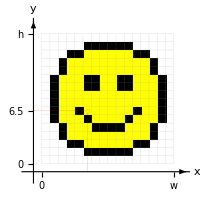

```mathematica
Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,5.5,{16,HoldForm[w]}},
{0,6.5,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{Red,Thickness[0],
Line[{{-1,6.5},{5.25,6.5}}],Line[{{5.5,6.25},{5.5,-1}}],
Circle[{5.5,6.5},1/4]}
}
,ImageSize->200]
```

Image pixels are covered by intervals between successive integer coordinate values. Thus, noninteger coordinates refer unambiguously to a single pixel. Integer coordinates located on pixel boundaries, however, take all immediate pixel neighbors into account, either by selecting all neighboring pixels or by taking their average color value.

Wolfram Language functions that focus on images adhere to image coordinates.

The color value at coordinate (x,y)=(5.5,6.5).

```mathematica
ImageValue[-Graphics-,{5.5,6.5}]
```

```mathematica
RGBColor[%]
```

You can select corner coordinates and select the region bordered by those pixels.

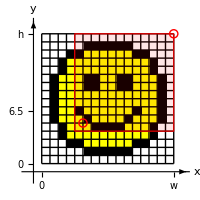

This allows you to trim “uninteresting” regions of an image.

```mathematica
ImageTrim[-Graphics-,{{5,5},{16,16}}]
```

ImageLines returns lines in standard image coordinates.

```mathematica
lines=ImageLines[GradientFilter[-Graphics-,1],0.1,0.05]
```

```mathematica
Show[-Graphics-,Graphics[{Green,Thickness[0.01],lines}]]
```

## Spatial Operations

The purpose of geometric transforms is to deform an image by altering its geometry.

A geometric operation T transforms a given image L into a new image L̃ by modifying the coordinates of image pixels; i.e. the value of the image Loriginally located at x⃗ moves to the position y⃗=T(x⃗) in the new image L̃:

L̃(y⃗)=L(T(x⃗))

Examples of geometric transformations:

```mathematica
ImageTransformation[-Graphics-,ReflectionTransform[{1,-1}]]
```

```mathematica
ImageTransformation[-Graphics-,x↦x^2]
```

## Spatial Operations

### Padding

Padding adds rows or columns to the outside of an image. There are many ways to determine the values of new pixels to be added to an image.

```mathematica
Panel[
TableForm[{
{"val", "pad with a constant value val"}, 
{"\"Fixed\"", "Cell["repetitions of the elements on each boundary", "TableText",ExpressionUUID->"32533d9a-649f-4ab1-8660-6040f5f55817"]"}, 
 {"\"Periodic\"", "cyclic repetitions of the complete array"}, 
{"\"Reflected\"", "reflections of the array in the boundary"}, 
{"\"Reversed\"", "reversals of the complete array"}}, 
TableHeadings -> {None, {"type", "description"}}, 
TableSpacing -> {1.5, 4}
],
BaseStyle -> "Text"
]
```

type | description
val | pad with a constant value val
"Fixed" | Cell["repetitions of the elements on each boundary", "TableText"]
"Periodic" | cyclic repetitions of the complete array
"Reflected" | reflections of the array in the boundary
"Reversed" | reversals of the complete array

Compare various padding methods.

```mathematica
With[
{paddings=Association@@Map[#-> ImagePad[-Graphics-, 100,#]&,{Green,"Fixed","Periodic","Reflected","Reversed"}]},Manipulate[paddings[pad],{{pad,First[Keys[paddings]]},Keys[paddings],ControlType->SetterBar}, SaveDefinitions->True]
]
```

Examples of a geometric transformation with padding:

```mathematica
ImageTransformation[-Graphics-,ReflectionTransform[{1,-1}], Padding-> "Fixed"]
```

## Spatial Operations

Two types of mappings are possible: source-to-target (forward) and target-to-source (backward).

### Forward Transforms

In the source-to-target approach, also known as forward transform, for every pixel position x⃗ in the source image, the corresponding transformed position in the target image is computed.

y⃗=T(x⃗)

The problem with this method is that, depending on the geometric transformation T, some elements in the target image may never receive a source pixel value. Conversely, a single pixel in the target image may be hit by multiple source pixels and, thus, image content may be lost. Due to all of these complications forward transforms are not the method of choice.

```mathematica
Show[
Rasterize[
GraphicsRow[{Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,12,{16,HoldForm[w]}},
{0,6.8,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{}
}
,ImageSize->240],
Graphics[{
Raster[ImageData[ImageCrop[ImageRotate[-Graphics-,20°, Padding-> White,Masking-> Full, Resampling-> "Linear"],ImageDimensions[-Graphics-]],DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,12.5,{16,HoldForm[w]}},
{0,8.5,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{Red,Thickness[0],Point[{12.5,8.5}]}
}
,ImageSize->240]},25],"Image"],
Graphics[{Red,Text[Style["T",Italic,24],{263.5,160}],Thickness[0.005],Arrow[BezierCurve[Reverse@{{451.5,134.5},{262.5,161.5},{179.5,115.5}}]]},Axes-> False]]
```

-Graphics-

In the source-to-target mapping there may be holes in the resulting image. To avoid creating large empty regions in the output you can perform interpolations to infer values of missing pixels.

Forward transform with no filling. Notice the black rows of pixels at the top and bottom of the resulting image.

```mathematica
img=-Graphics-;
```

```mathematica
ImageForwardTransformation[img,x↦x^2,Method->None,PlotRange->All]
```

Forward transform with filling.

```mathematica
ImageForwardTransformation[img, x↦x^2,Method->Automatic, PlotRange->All]
```

## Spatial Operations

### Backward Transforms

In the target-to-source case, also known as backward transform, every discrete pixel position y⃗ in the target image is mapped back via T^-1 to a corresponding point in the source image.

x⃗ = T^-1(y⃗)

Thus, all pixels in the target image are filled exactly once by corresponding interpolated values of the source. No holes or multiple hits can occur.

This mapping, however, requires the inverse geometric transformation T^-1.

```mathematica
Show[
Rasterize[
GraphicsRow[{Graphics[{
Raster[ImageData[-Graphics-,DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,12,{16,HoldForm[w]}},
{0,6.8,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{}
}
,ImageSize->240],
Graphics[{
Raster[ImageData[ImageCrop[ImageRotate[-Graphics-,20°, Padding-> White,Masking-> Full, Resampling-> "Linear"],ImageDimensions[-Graphics-]],DataReversed-> True]], 
{Antialiasing -> False,Thickness[0], GrayLevel[GoldenRatio-1], 
Line[Table[{{0, k}, {16, k}},{k,0,16}]],
Line[Table[{{k, 0}, {k, 16}},{k,0,16}]]}
}, 
Axes-> True,
PlotRange-> {{-2,17.5},{-2,17.5}},
AxesOrigin->{-1,-1},
AxesLabel-> {"x","y"} ,
Ticks->{
{0,12.5,{16,HoldForm[w]}},
{0,8.5,{16,HoldForm[h]}}
} , 
Epilog -> {
Arrow[{{17.4,-1},{17.5,-1}}],
Arrow[{{-1,17.4},{-1,17.5}}],
{Red,Thickness[0],Point[{12.5,8.5}]}
}
,ImageSize->240]},25],"Image"],
Graphics[{Red,Text[Style["T^-1",Italic,24],{263.5,160}],Thickness[0.005],Arrow[BezierCurve[{{451.5,134.5},{262.5,161.5},{179.5,115.5}}]]},Axes-> False]]
```

-Graphics-

Here is an example of the same transformation x↦√x computed by the backward transform:

```mathematica
ImageTransformation[-Graphics-,x↦√x,PlotRange->All, Padding->"Fixed"]
```

## Spatial Operations

### Interpolation Schemes

Interpolation is the process of estimating the continuous function from a set of discrete samples. This task arises from the fact that pixel positions in one image are usually not mapped to discrete positions in the other image when a continuous geometric transformation is applied. Via interpolation you can obtain optimal estimates for the intermediate values that preserve as much image detail as possible without introducing visible artifacts. There are many possible interpolation methods.

#### Nearest Neighbor

The simplest of all interpolation methods is to round the continuous coordinate x to the nearest integer coordinate u, with u=Floor[x+1/2]. It is called the nearest-neighbor interpolation. It is known that nearest-neighbor interpolation causes strong blocking effects, so it is rarely used for geometric transformations but it is useful when one wants to enlarge an image without any smoothing.

#### Linear

Another simple method is linear interpolation. It is also known as bilinear interpolation (2D images) or trilinear interpolation (3D images). Linear interpolation can be expressed as a linear convolution. The convolution kernel for linear interpolation is defined as:

K_linear(x)=Piecewise[{{x+1, -1<x≤0}, {1-x, 0<x<1}, {0, True}}]

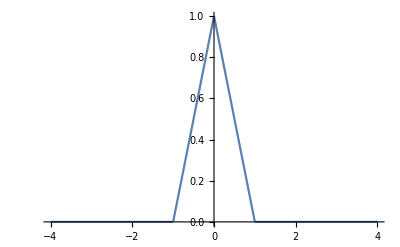

#### O-MOMS

The O-MOMS are a family of basic functions that achieve optimal interpolation of maximal order with minimal support. These functions can be expressed as the weighted sum of a B-spline and its derivatives. The convolution kernel for the O-MOMS interpolation of order 3 is defined by:

oMOMS_3x=x↦(∑_(k=-∞)^∞ √(21/5) (1/8 (√105-13))^Abs[k])  1/42 Piecewise[{{(2-k+x) (29+7 (-k+x) (4-k+x)), -2≤-k+x<-1}, {(26-3 (-k+x) (1+7 (-k+x) (2-k+x))), -1≤-k+x≤0}, {(26+3 (-k+x) (1+7 (-2-k+x) (-k+x))), 0<-k+x<1}, {-(-2-k+x) (29+7 (-4-k+x) (-k+x)), 1≤-k+x≤2}, {0, True}}]

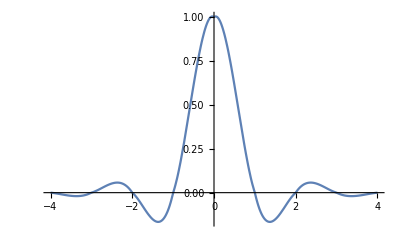

#### Other Interpolation Schemes

All possible interpolation schemes available in the Wolfram Language are described on the Resampling reference page. They can be divided into six categories: nearest neighbors, spline interpolations, Gaussian and B-splines, classic polynomial interpolations, O-MOMS interpolations, and windowed sinc interpolations. Here are some properties of various interpolation schemes:

```mathematica
Module[
{types,props},
types={"Linear", "Keys", "Parzen", "Lanczos", "Cubic", {"OMOMS", 3}};props={#,ResamplingAlgorithmData[#, "Kernel"], ResamplingAlgorithmData[#, "Regularity"],  ResamplingAlgorithmData[#, "BasisSupport"], 10Log[10,0.9786575/(1/π Quiet@NIntegrate[Evaluate[(-2 Log[0.9])/(ω^2+(Log[0.9])^2)*ResamplingAlgorithmData[#,"ErrorKernel"][ω]],{ω,0,π}])]}&/@types;
Manipulate[Magnify[Plot[{Re@(props[[i,2]])[x]/.∞->16,Sinc[π x]},{x,-2,4},PlotRange->{-0.3,1.1},Ticks->{Range[-2,4,1],{0,1}},PlotStyle->{Black,Dashed},Filling->Axis,Epilog->{Style[Text[ToString[props[[i,1]]],{1,0.93},{-1,0}],Bold],Text["regularity "<>"\!\(\*
        StyleBox[\"C\",\nFontSlant->\"Italic\"]\)"^ToString[props[[i,3]]],{1,0.8},{-1,0}],Text["support radius = "<>ToString[props[[i,4]]],{1,0.7},{-1,0}],Text["SNR = "<>ToString[props[[i,5]]],{1,0.6},{-1,0}]}],1.2],{{i,1,""},Thread[Range[Length[types]]->types],ControlType->SetterBar}, SaveDefinitions->True]
]
```

Impact of the interpolation method on the transformation result after 18 consecutive rotation steps of 10°:

```mathematica
With[
{img = -Graphics-},
TabView[{
"Linear"->Nest[ImageRotate[#,10°, 512]&,img,18],
"Cubic o-MOMS"->Nest[ImageRotate[#,10°, 512, Resampling-> {"OMOMS",3}]&,img,18]
}]
]
```

12

## Spatial Operations

### Leaning Tower of Pisa

```mathematica
img=-Graphics-;
```

Determine the 16 most prominent straight lines in the image:

```mathematica
lines = ImageLines[GradientFilter[img,2],MaxFeatures->16]
```

```mathematica
HighlightImage[img,lines]
```

Rotate the image by the average angle of nearly vertical lines:

```mathematica
ImageRotate[
img,
Median@Select[Map[VectorAngle[#,{0,1}]&,Apply[Subtract,Sequence@@@lines,{1}]],(-10°<#<10°)&], 
"MaxAreaCropping"
]
```

## 3D Reconstruction

### Focal Stacking

You can combine differently focused images of the same scene to obtain a single well-focused image:

```mathematica
stack={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
ListAnimate[stack]
```

```mathematica
ImageFocusCombine[stack]
```

Furthermore, the focal length information allows you to create a depth map and a 3D reconstruction:

```mathematica
focusResponses=
Map[
ImageNorm@LaplacianGaussianFilter[#,{3,1}]&,
stack
];
```

```mathematica
depthVol=MaxChannelSuppression[focusResponses];
```

```mathematica
inFocus=ImageAdd@@MapThread[ImageMultiply,{stack,depthVol}]
```

```mathematica
depthMap1=ImageAdjust[ImageAdd@@MapIndexed[ImageMultiply[#1,First[#2]]&,depthVol]]
```

Only consider the depth map values with high confidence:

```mathematica
confindenceMap=ImageAdd@@MapThread[ImageMultiply[Image`ImageDivide[#1,ImageAdd[ColorConvert[#2,"Grayscale"],0.2]],#3]&,{focusResponses,stack,depthVol}];
```

```mathematica
ImageAdjust[confindenceMap]
```

```mathematica
depthMap2=ImageMultiply[depthMap1,Binarize[confindenceMap,0.02]]
```

Fill any holes in the depth map:

```mathematica
depthMap3=FillingTransform@MedianFilter[depthMap2,3]
```

Display the image in 3D:

```mathematica
ListPlot3D[
Reverse@ImageData[Blur@ImageResize[depthMap3,Scaled[1/8]]],
InterpolationOrder->1, 
PlotStyle->Texture[SetAlphaChannel[inFocus,Binarize[depthMap3,0.1]]] , 
Mesh-> False,
Lighting->{{"Ambient",White}},
Axes-> None,
BoxRatios->{1,ImageAspectRatio[depthMap3],1/3},
ImageSize-> 640
]
```

## Morphology

Morphology deals with spatial structures, the shape and form of objects.

### Erosion

Erosion, denoted as L⊖𝓈 or ϵ_𝓈(L), is one of two fundamental operators of mathematical morphology.

Binary erosion is a neighborhood operation such that the result at location x⃗ is a pointwise OR operation of samples of L with samples of the pointwise complement of 𝓈 (when centered on x⃗) followed by AND. Effectively, this is a minimum over L(𝓈_(x⃗)).

ϵ_𝓈: L(x⃗)↦(m i n)_(y⃗∈ 𝓈_(x⃗)) (L(y⃗))

Erosion is similar in effect to a fitting operation. Namely, does 𝓈 fit inside the object being probed?

```mathematica
A=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0}, {0, 0, 1, 1, 1, 1, 0}, {0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0}});ker=({{0, 0, 0}, {0, 1, 1}, {0, 0, 1}});
r=Rasterize[Row[{Style[GraphicsGrid[A,BaseStyle->{Bold,Medium},ImageSize->200],Antialiasing->False],Style[GraphicsGrid[Erosion[A,ker],BaseStyle->{Bold,Medium},ImageSize->200],Antialiasing->False]},Spacer[40]],"Image"];
line1=Line[{{59+30,120},{59+30,198},{140+30,198},{140+30,120},{59+30,120}}];
pol1=Polygon[{{143,120},{143,145},{113,145},{113,172},{170,172},{170,120}}];
circ11=Disk[{98.+30,160.},9];
arr1=Arrow[BezierCurve[{{106.+30,152.},{232.+30,118.},{340.+30,160.}}]];
line2=Line[{{196-60.,36.},{119-60.,36.},{119-60,113.},{196.-60,113.},{196.-60,36.}}];
pol2=Polygon[{{110,36},{110,60},{80,60},{80,90},{136,90},{136,36}}];
cric21=Disk[{158.-60,74.},9];
arr2=Arrow[BezierCurve[{{165.-60,68.},{288.-60,30.},{405.-60,74.}}]];
Show[{r,Graphics[{{Dashed,line1,line2},{Opacity[0.25],pol1,pol2},{Red,Text[Style["⊖",15],{225,150}],arr1,arr2,Opacity[0.5],circ11,cric21}}]},ImageSize->360]
```

-Graphics-

#### Erosion Using Different Shapes

Erode a binary image using three differently shaped structuring elements: , , and .

```mathematica
img=-Graphics-;
erode=Table[Erosion[img,ker],{ker,{BoxMatrix[1],BoxMatrix[{0,2}],BoxMatrix[{2,0}]}}];
GraphicsRow[Table[HighlightImage[img,i,Method->"Solid","HighlightColor"->Magenta],{i,erode}]]
```

-Graphics-

#### Erosion Using Different Sizes

Erosion using a variable-size disk-shaped structuring element of radius r.

```mathematica
DynamicModule[
{img=-Graphics-},
Manipulate[ColorCombine[{img,Erosion[img,DiskMatrix[radius]],img}],{{radius,5},0,16}]]
```

## Morphology

### Dilation

Dilation, denoted as L⊕𝓈 or δ_𝓈(L), is one of two fundamental operators of mathematical morphology.

Binary dilation is a neighborhood operation such that the result at location x⃗ is a pointwise AND operation of samples of L with those of 𝓈 (when centered on x⃗), followed by OR. Effectively, this is a maximum over L(𝓈_(x⃗)).

δ_𝓈: L(x⃗)↦(m a x)_(y⃗∈ 𝓈_(x⃗)) (L(y⃗))

```mathematica
A=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0}, {0, 0, 1, 1, 1, 1, 0}, {0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0}});ker=({{0, 0, 0}, {0, 1, 1}, {0, 0, 1}});
r=Rasterize[Row[{Style[GraphicsGrid[A,BaseStyle->{Bold,Medium},ImageSize->200],Antialiasing->False],Style[GraphicsGrid[Dilation[A,ker],BaseStyle->{Bold,Medium},ImageSize->200],Antialiasing->False]},Spacer[40]],"Image"];
line=Line[{{59,120},{59,198},{140,198},{140,120},{59,120}}];
pol=Polygon[{{113.,120.},{113.,146.},{87.,146.},{87.,175.},{140.,175.},{140.,120.}}];
dsk=Disk[{98.,160.},9];
arr=Arrow[BezierCurve[{{106.,152.},{232.,118.},{340.,158.}}]];
Show[{r,Graphics[{{Dashed,line},{Opacity[0.25],pol},{Red,Text[Style["⊕",15],{225,150}],arr,Opacity[0.5],dsk}}]},ImageSize->360]
```

-Graphics-

#### Apply Different Shapes

Dilate a binary image using three differently shaped structuring elements: , , and .

```mathematica
img=-Graphics-;
dilate=Table[Dilation[img,ker],{ker,{BoxMatrix[1],BoxMatrix[{0,2}],BoxMatrix[{2,0}]}}];
GraphicsRow[Table[HighlightImage[i,ImageSubtract[i,img],Method->"Solid","HighlightColor"->Green],{i,dilate}]]
```

-Graphics-

#### Apply Different Sizes

Observe the effect of varying the size of a disk-shaped structuring element of radius r.

```mathematica
DynamicModule[
{img=-Graphics-},
Manipulate[ColorCombine[{img,Dilation[img,DiskMatrix[r]],img}],{{r,5,Style["r",Italic]},0,16}]]
```

## Morphology

Dilation and erosion can be used to find important object features such as borders and edges.

### Inner Border

The inner border is defined as the difference between an object and its erosion.

β_inner(L)=L-L⊖𝓈

Use erosion to find the inner border.

```mathematica
a=-Graphics-;e=Erosion[a,1];βi=ImageSubtract[a,e];
Show[HighlightImage[a,βi,Method->"Solid","HighlightColor"->Magenta],ImageSize->240]
```

This effectively is MorphologicalPerimeter.

```mathematica
MorphologicalPerimeter[a]
```

### Outer Border

The outside border (or contour) β_outer of an object f is the difference between a dilation of the object and itself.

β_outer(L)=L⊕𝓈-L

Use dilation to find the outer border.

```mathematica
a=-Graphics-;d=Dilation[a,1];βo=ImageSubtract[d,a];
Show[HighlightImage[a,βo,Method->"Solid","HighlightColor"->Green],ImageSize->240]
```

## Morphology

### Opening

Dilation and erosion are often applied to an image in concatenation.

Erosion followed by dilation is called an open operation.

L 𝓈 ◦=(L⊖𝓈)⊕𝓈

```mathematica
f=ImageData[-Graphics-];
ker={{1,1,0},{1,1,0},{0,0,0}};
GraphicsRow[MapThread[Labeled[ArrayPlot[#1,ColorRules->{1->White,0->Black},Mesh->True],#2]&,{{f,Erosion[f,ker],Dilation[Erosion[f,ker],ker]},{"L","L ⊖ 𝓈","( L ⊖ 𝓈 ) ⊕ 𝓈"}}],ImageSize->{Automatic,220}]
```

-Graphics-

## Morphology

### White Top-Hat Filter

The white top-hat filter enhances positive peaks. The filter returns the difference between the original image and its opening.

WTH(L)=L-L 𝓈 ◦

Erosion followed by dilation is called an open operation.

L 𝓈 ◦=(L⊖𝓈)⊕𝓈

A white top-hat filter can be useful in eliminating an uneven background in an image.

Remove the uneven background from the image by extracting white peaks.

```mathematica
DynamicModule[{books},books=-Graphics-;Manipulate[GraphicsRow[{Labeled[books,"L",ImageMargins->5],Labeled[Opening[books,r],"L◦𝓈",ImageMargins->5],Labeled[TopHatTransform[books,r],"WTH(L)",ImageMargins->5]},Scaled[0.05],ImageSize->640],{r,0,21,1}]]
```

## Filters and Features

Image processing filters are functions that take an image as input and return an image as output. You can apply filters for noise removal, image enhancement and feature extraction.

### Gaussian Filter

Convolve an image with a Gaussian kernel G_σ to remove all the high-resolution detail:

G_σ(x,y)= Piecewise[{{1/(2 π σ^2) exp(-(x^2+ y^2)/(2 σ^2)), for |x|≤r and |y|≤r}, {0, otherwise.}}]

```mathematica
Manipulate[
With[{r = 3σ},GaussianFilter[-Graphics-,{σ,r}]],
{σ,0.5,16}
]
```

## Filters and Features

### Scale Space

For t=σ^2/2, the Gaussian kernel is the point spread function (also known as Green’s function) of the diffusion equation ∂_t G_t = Δ G_t. Thus, the convolution G_t ⋆ L returns the diffusion of luminosity after time t with the initial condition given by the input image L. By the way, you can interpret the preceding as the diffusion of luminosity/brightness or as the diffusion of black ink/darkness, since both G_t ⋆ L and G_t ⋆ (1-L) satisfy the diffusion equation.

Stacking up the images of this time evolution results in a so-called scale space. The time axis t runs up vertically, the bottom layer is the original image with all details, and the preceding layers only contain the coarser features larger than a given scale σ=√(2t).

Scale space volume of the fox image (use the Crop Tool of the image bar to view the layers).

```mathematica
Image3D[
Table[GaussianFilter[-Graphics-,√(2t){3,1}],{t,64,0,-1}],
"Byte",
ColorFunction:> (Blend[{{0., RGBColor[0., 0., 0., 0.1]}, {1., RGBColor[1., 1., 1., 0.]}}, #1]&),
Axes-> True,
AxesLabel->{"x","y","t"},
BoxRatios-> {240,136,128}
]
```

## Filters and Features

### DoG and Laplacian Filter

To extract the image features L_σ at a particular scale σ=√(2t), you have to determine the image portion that is lost as one moves from one scale space layer to the one preceding.

L_σ = G_t ⋆ L - G_(t+Δt) ⋆ L = (G_t - G_(t+Δt)) ⋆ L

To obtain the features in the scale layer between σ and σ', you have to apply a filter kernel that consists of the difference of Gaussians G_σ'-G_σ, the so-called DoG filter.

The DoG-filtered fox image. At small scales, the fur and teeth are visible. Large scales render the posture of the fox.

```mathematica
Manipulate[
ImageAdjust@ImageSubtract[GaussianFilter[-Graphics-,√(2t){3,1}],GaussianFilter[-Graphics-,√(2(t+Δt)){3,1}]],
{{t,1},0.1,64},
{{Δt,1},0.1,4}
]
```

To obtain the features of an infinitesimally thin scale layer, you have to consider the partial derivative of Gaussian ∂_t G_t|_(t=σ^2/2) with respect to t, resulting in the negative Laplacian of Gaussian filter with kernel ΔG_σ.

ΔG_σ(x,y)= Piecewise[{{(x^2+y^2-2 σ^2)/(2 π σ^6) exp(-(x^2+ y^2)/(2 σ^2)), for |x|≤r and |y|≤r}, {0, otherwise.}}]

The negative Laplacian of Gaussian filter applied to the fox image. This filter returns the same results as the DoG filter for very small Δt.

```mathematica
Manipulate[
ImageAdjust@ColorNegate@LaplacianGaussianFilter[-Graphics-,√(2t){3,1}],
{t,0.1,64}
]
```

## Filters and Features

### Image Derivatives

You cannot obtain the partial derivative of a digital image in a straightforward manner. Due to the finite pixel size, the limit lim_(h→0) (L(x+h)-L(x))/h is not properly defined. However, it is possible to determine the filter output of an image derivative. Note that for a differentiable kernel function k with finite support, the following two convolutions are equivalent (see Proof).

k ⋆ L'=k' ⋆ L

In other words, knowing the partial derivative k' of a filter kernel k, you can obtain the filter result for L'. Hence, you are in a position to determine the image derivatives at given scales.

Convolve an image with a Gaussian kernel at scale σ to exhibit all features at scales > σ.

```mathematica
img=-Graphics-;
Manipulate[GaussianFilter[img,σ{3,1},{0,0}],{σ,0,8}]
```

Convolution of an image with the x derivative of a Gaussian kernel at scale σ. This exhibits the x derivative of features at scales > σ.

```mathematica
Manipulate[ImageAdjust@GaussianFilter[img,σ{3,1},{0,1}],{{σ,1},1,12}]
```

Convolve an image with a negative Laplacian of Gaussian kernel at scale σ to exhibit all features at scales = σ.

```mathematica
Manipulate[ImageAdjust@ColorNegate@LaplacianGaussianFilter[img,σ{3,1}],{σ,1,12}]
```

Convolution of an image with the x derivative of a negative Laplacian of Gaussian kernel at scale σ. This exhibits the x derivative of features at scales = σ.

```mathematica
Manipulate[ImageAdjust@ColorNegate@ImageAdd[GaussianFilter[img,σ{3,1},{2,1}],GaussianFilter[img,σ{3,1},{0,3}]],{{σ,1},1,12}]
```

Obviously, you can only obtain reliable image derivatives at scales σ equal to or larger than the image pixel size.

## Filters and Features

### Edges

At edges, the gradient amplitude of the luminosity function L is high:

```mathematica
GradientFilter[-Graphics-,2]//ImageAdjust
```

### Corners

At corners one encounters a large derivative in two directions.

This results in two large eigenvalues of the structure matrix (L_x^2 | L_x L_y
L_x L_y | L_y^2) .
The minimum of the structure matrix is, hence, a good corner feature:

```mathematica
CornerFilter[-Graphics-,2]//ImageAdjust
```

```mathematica
ImageCorners[-Graphics-,2,MaxFeatureDisplacement->0,MaxFeatures->10]
```

### Feature Points

Similarly to corner detection, a keypoint operator first computes a response map in a 3D space {x, y, σ}, where x and y correspond to changes along spatial directions and σ to changes along scale. Various criteria, such as asymmetry in local curvature, may be used for the computation of the response map.

Then keypoints are detected by finding local maxima of the response map in this 3D space.

In this example you can see the result of keypoint detection using the SURF algorithm. Circle sizes correspond to scales.

```mathematica
img=-Graphics-;
points=ImageKeypoints[img,{"Position","Scale"},MaxFeatures->100];
Show[img,Graphics[Table[{{White,Circle[p[[1]],p[[2]]*2.5]}},{p,points}]]]
```

## Filters and Features

### Registration

Two images to be stitched together:

```mathematica
img1 =ImageAdjust@ -Graphics-;
```

```mathematica
img2=ImageAdjust@ -Graphics-;
```

Find corresponding landmarks in both images:

```mathematica
pts=ImageCorrespondingPoints[img1,img2,KeypointStrength-> 0.001]
```

```mathematica
MapThread[HighlightImage[#1,#2, ImageSize-> Scaled[1/3]]&,{{img1,img2},pts}]
```

Determine the perspective transformation that maps the key-points in the second image into the key-points of the first image:

```mathematica
{error,trafo}=FindGeometricTransform@@pts
```

Use the perspective transformation to project the second image into the first:

```mathematica
{w1,h1}=ImageDimensions[img1];{w2,h2}=ImageDimensions[img2];
tmp=ImagePerspectiveTransformation[img2,trafo,DataRange->Full,PlotRange->{{0,First@trafo[{w2,0}]},{0,h1}}, Padding-> Transparent]
```

```mathematica
stitch=ImageCompose[tmp,{img1,1},{0,0},{0,0}]
```

Create a mask for the missing upper-right corner:

```mathematica
mask=Dilation[Binarize@ColorNegate@AlphaChannel[stitch],2];
```

In-paint the missing part of the image:

```mathematica
Inpaint[RemoveAlphaChannel[stitch],mask]
```

## Filters and Features

### Gabor Filter

The Fourier transform of a textile image ℱ(L) visualized via a periodogram.

```mathematica
img=Image[-Graphics-, Magnification->2];
```

```mathematica
ImagePeriodogram[img]
```

The periodic pattern of the textile amounts to a grid of peaks in Fourier space.

The Fourier transform of a Gabor filter kernel ℱ(k) has similar properties. It exhibits two peaks opposite each other.

```mathematica
cosGaborKernel=Image@GaborMatrix[20{5,1},0.75{Cos[51°],-Sin[51°]},0 ];
sinGaborKernel=Image@GaborMatrix[20{5,1},0.75{Cos[51°],-Sin[51°]},π/2 ];
GraphicsRow[{ImageAdjust@cosGaborKernel,ImageAdjust@sinGaborKernel}]
```

```mathematica
GraphicsRow[{ImageAdjust@ImagePeriodogram@cosGaborKernel,ImageAdjust@ImagePeriodogram@sinGaborKernel}]
```

By multiplying the Fourier transform ℱ(k) of the Gabor kernel with the Fourier transform ℱ(L) of the textile image, you can single out the peaks that are caused by the textile pattern.

```mathematica
HighlightImage[ImagePeriodogram[img],ImagePeriodogram[sinGaborKernel]]
```

Combining the sin and cos versions of the Gabor filter.

```mathematica
mask=ImageAdjust[
GaborFilter[img,20{5,1},0.75{Cos[51°],-Sin[51°]},0, Padding-> "Periodic"]^2+
GaborFilter[img,20{5,1},0.75{Cos[51°],-Sin[51°]},π/2, Padding-> "Periodic"]^2
]
```

The peaks in the Fourier space belong to just one of the two textile patterns in the image. The Gabor filter is suited to extract that discriminating feature.

```mathematica
HighlightImage[img,Binarize[mask]]
```

## Image Recognition

### Barcodes

```mathematica
image=-Graphics-;
```

Features: Responses to horizontal and vertical derivative filters
Processing: Detection of regions with consistent gradient magnitude and orientation

```mathematica
bc=BarcodeRecognize[image,{"BoundingBox","Data","Format"}];
Show[image,Graphics[{EdgeForm[{AbsoluteThickness[1],Yellow}], FaceForm[],Rectangle@@bc[[1]], Inset[Style[bc[[2]]<>"\n"<>bc[[3]],Bold,Yellow,FontSize->20], RegionCentroid[Rectangle@@bc[[1]]]]}]]
```

### Text Recognition

```mathematica
image=-Graphics-;
```

Features: Sequence of individual blobs in a row
Processing: Classification in characters and words

```mathematica
TextRecognize[LocalAdaptiveBinarize[image,40,{0.85,0.07}]]
```

## Segmentation

### Connected Components

In region-based segmentation algorithms, pixel locations and their connectivity are also taken into account.

Connected-components labeling is one of the simple segmentation techniques used for labeling connected pixels. This algorithm is ideal for labeling non-overlapping foreground components. It creates a partitioning of foreground pixels.

```mathematica
img=-Graphics-
```

Separate foreground from background.

```mathematica
Binarize[img,{0,.9}]
```

Label each connected component and visualize each with a distinct color.

```mathematica
cc=MorphologicalComponents[Binarize[img,{0,.9}]];
Colorize[cc]
```

Compute shape and color value properties for each component.

```mathematica
ds=Dataset[Association@@MapThread[Rule,{props,#}]&/@ComponentMeasurements[{cc,img},props={"Shape","Mean","Count","Centroid","Elongation"}][[All,2]]];
SortBy[ds[All,{"Shape"->Function[{image},ImagePad[image,10,0]],"Mean"->RGBColor}],#Elongation&]
```

## Segmentation

### Region Growing

A region-growing algorithm starts from one or multiple seed points and grows as long as the values of neighboring pixels do not exceed the given threshold.

```mathematica
img=-Graphics-;
```

Start from a single seed point.

```mathematica
Manipulate[SetAlphaChannel[img,ColorNegate[RegionBinarize[img,{{400,100}},t]]],{t,0,1,Appearance->"Labeled"}]
```

Start from multiple seed points.

```mathematica
markers={{6,300},{6,76},{270,290},{234,132},{146,104},{98,336},{82,288},{76,272},{214,314},{88,48},{396,74}};
Manipulate[SetAlphaChannel[img,ColorNegate[RegionBinarize[img,markers,t]]],{t,0,.5,Appearance->"Labeled"}]
```

You can superimpose the detected foreground on a different background.

```mathematica
ImageCompose[-Graphics-,SetAlphaChannel[img,ColorNegate[RegionBinarize[img,{{6,300},{6,76},{270,290},{234,132},{146,104},{98,336},{82,288},{76,272},{214,314},{88,48},{396,74}},.3]]]]
```

## Segmentation

### Watershed Algorithm

The watershed segmentation seeks the water basins in a given "gradient" mountain range.

Example: Heart chamber segmentation.

```mathematica
img=-Graphics-;
```

```mathematica
ListPlot3D[ImageData[GradientFilter[img,3],DataReversed-> True], PlotRange-> All, BoxRatios-> {1,1,1/10}, Boxed-> False, Mesh-> False,ColorFunction-> "AlpineColors", Axes-> None]
```

Smooth the gradient image by filling shallow holes and compute basins.

```mathematica
WatershedComponents[FillingTransform[GradientFilter[img,3],.07]]//Colorize
```

Find some marker points using local maxima of smoothed data.

```mathematica
markers=MaxDetect[GaussianFilter[img,25],Padding->1];
HighlightImage[img,markers,Method->{"DiskMarkers",5}]
```

Watershed segmentation using detected marker points.

```mathematica
WatershedComponents[GradientFilter[img,3],markers]//Colorize
```

## Segmentation

### Grow-Cut Algorithm

Creating a marker image is a common step among many segmentation algorithms. There are various ways of generating these markers: manually or programmatically.

The Wolfram Language provides a marker generation tool in the toolbar attached to every image. Marker positions for an image including marker pixels can be specified using the toolbar.

As an example, you can segment the foreground from the background of an image using grow-cut segmentation.

```mathematica
image=-Graphics-;
```

Interactively generated markers.

```mathematica
background=-Graphics-;foreground=-Graphics-;
```

Segment foreground from background using grow-cut segmentation.

```mathematica
mask=Image[GrowCutComponents[image,{background,foreground}]-1]
```

```mathematica
SetAlphaChannel[image,mask]
```

## Segmentation

### Active Contours

The Chan–Vese segmentation is a segmentation based on active contours. The algorithm segments an image domain Ω into two segments 𝒟 (foreground) and Ω\𝒟 (background) with contour Γ==∂𝒟 and minimizes the following functional F of image f:

F(c_1,c_2,Γ) = μ Length(Γ)+νArea(𝒟)+λ_1∫_𝒟 Abs[f-c_1]^2 ⅆxⅆy+λ_2∫_(Ω\𝒟) Abs[f-c_2]^2 ⅆxⅆy

The function is parametrized by the length penalty μ, the area penalty ν, and level penalties λ_1 and λ_2. The algorithm partitions images such that the foreground and background will differ from constant colors c_1 and c_2 as little as possible, respectively. Foreground and background colors can be specified or automatically computed.

```mathematica
ChanVeseBinarize[-Graphics-]
```

Specify the foreground color.

```mathematica
ChanVeseBinarize[-Graphics-,Orange]
```

Specify both foreground and background colors for creating an initial marker.

```mathematica
ChanVeseBinarize[-Graphics-,{{Yellow,Brown}}]
```

Penalty parameters can also be fine-tuned to achieve a better segmentation. For instance, increasing the penalty for the boundary length of the Ω\𝒟 segment can improve segmentation of a noisy image.

```mathematica
Manipulate[ChanVeseBinarize[-Graphics-,Automatic,{μ}],{μ,0,1}]
```

## Summary

Hopefully this talk will help you to navigate through the domain of image processing.

A quick approach to solving a maze.

```mathematica
maze=-Graphics-;
```

Via watershed, one can find the basins to the left and right side of the path that connects the entry and the exit of the maze.

```mathematica
WatershedComponents[Binarize[maze,0.01]]//Colorize
```

Thus, the water divide is the solution.

```mathematica
path=Image[WatershedComponents[Binarize[maze,0.01]] ,"Bit"]
```

Visualizing the result.

```mathematica
ImageApply[List@@Purple&, maze, Masking -> ColorNegate[path]]
```

## Q & some A

## Initialization

### ImageNorm

```mathematica
ImageNorm=img↦Image`ImagePower[ImageAdd@@ColorSeparate[Image`ImagePower[img,2]],1/2];
```

### MaxChannelSuppression

```mathematica
MaxChannelSuppression[list:{__Image}]:=
ImageMultiply@@@Partition[
Map[(Binarize[#, 0]&)@*ImageSubtract, Permutations[list, {2}]], 
Length[list] - 1
]
```